## Invoice

Getting the data from the invoice.csv file (may take a few seconds)

We import the Data from the invoice.csv file,

Take the headers from the first row of the csv file

build a list of associations(Key-Value datastructures) to be fed into a Dataset

Create a Dataset (like dataframe from pandas) invoice

```mathematica
csv=Import[FileNameJoin[{NotebookDirectory[],"data_code","invoice.csv"}]];
headers=First[csv];
assoc=Association[Thread[headers->#]]&/@Rest[csv];
invoice=Dataset[assoc];
Clear[assoc]
```

Getting the data from the items.csv

We import the Data from the item.csv file,

Take the headers from the first row of the csv file and call it headersItem

build a list of associations(Key-Value datastructures) to be fed into a Dataset

Create a Dataset (like dataframe from pandas) item

```mathematica
csvItem=Import[FileNameJoin[{NotebookDirectory[],"data_code","item.csv"}]];
headersItem=First[csvItem];
assocItem=Association[Thread[headersItem->#]]&/@Rest[csvItem];
item=Dataset[assocItem];
Remove[assocItem]
```

Getting the data from the review.csv (put together using datMerger.nb)

We import the Data from the review.csv file,

Take the headers from the first row of the csv file and call it headersItem

build a list of associations(Key-Value datastructures) to be fed into a Dataset

Create a Dataset (like dataframe from pandas) item

```mathematica
csvReview=Import[FileNameJoin[{NotebookDirectory[],"reviews","review.csv"}]];
headersReview=First[csvReview];
assocReview=Association[Thread[headersReview->#]]&/@Rest[csvReview];
review=Dataset[assocReview];
Remove[assocReview]
```

Here we look at the lengths of the datasets

```mathematica
{Length[invoice],Length[item],Length[review]}
```

{930508,4166,50000}

and the names of the headers for each

```mathematica
headers
```

{Invoice_id,Date,Item_id,Vendor_id,Vendor_Name,Store_id,Store_Name,Address,City_Name,Zip_Code,County_id,County_Name,Bottles_Sold}

```mathematica
headersItem
```

{Item_id,Item_Description,Category,Pack,Bottle_Volume_ml,Bottle_Cost,Bottle_Retail_Price}

```mathematica
headersReview
```

{Customer_id,Invoice_id,Product_Rating}

we see that invoice and item share the “Item_Id” tag so we would like to merge them into one, Using JoinAccross.  This takes a few seconds.

```mathematica
itemInvoice=JoinAcross[invoice,item,"Item_id"];
```

The following is an example on how to add a new column keyed under “Purchase_Cost” obtained from the product of the “Bottles_Sold” value with the “Bottle_Retail_Price”.

```mathematica
RandomChoice[itemInvoice]/.x_Association:>Association[x,"Purchase_Cost"->x["Bottle_Retail_Price"] x["Bottles_Sold"]]
```

We can do the above to the whole mixed Dataset (takes a few seconds)

```mathematica
withPurchaseCost=(itemInvoice/.x_Association:>Association[x,"Purchase_Cost"->x["Bottle_Retail_Price"] x["Bottles_Sold"]]);
```

We can see with an example what the result looks like. Pay special attention to the Purchase_Cost

```mathematica
RandomChoice[withPurchaseCost]
```

The length of the latest Dataset should be the same as the one from the original invoices

```mathematica
Length[withPurchaseCost]==Length[invoice]
```

True

### Invoice

We can look at the cities surveyed

```mathematica
invoice[Counts,"City_Name"]
```

Since they are only two an interesting analysis would be to separate them and look at their respective statistics maybe we will come back to that later

We can take out a count by date (# of purchases per day)

```mathematica
invoice[Counts,"Date"]
```

And get a time series plot

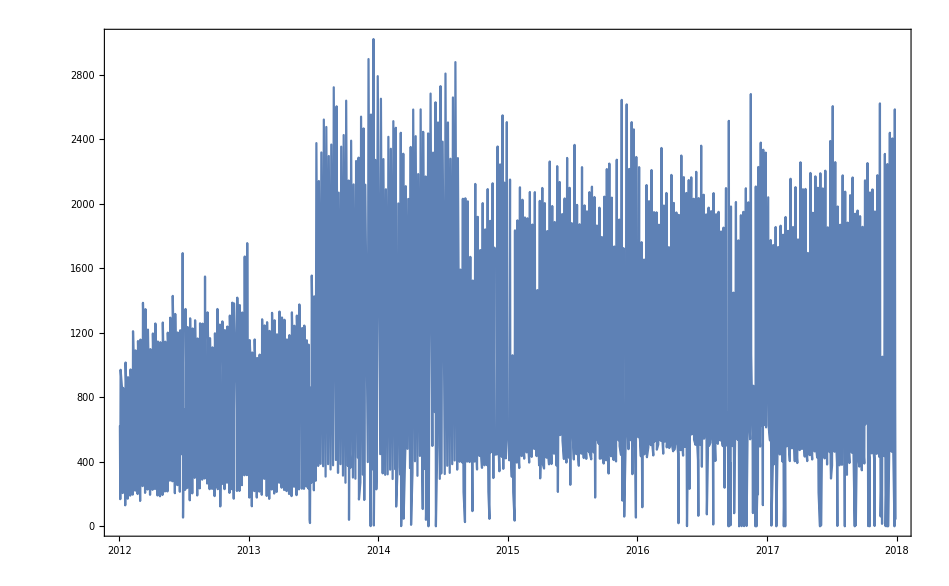

```mathematica
DateListPlot[invoice[Counts,"Date"]]
```

The above is interesting, as it shows that something occurred around mid-2013 that shot sales per day up.

We can look at a moving average to see more general trends.

```mathematica
MovingAverage[Values[invoice[Counts,"Date"]]//Normal,5]
```

1017

```mathematica
(Keys[invoice[Counts,"Date"]]//Normal)[[5;;]]//Length
```

1017

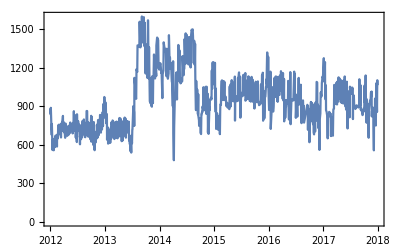

```mathematica
DateListPlot[Association[Thread[(Keys[invoice[Counts,"Date"]]//Normal)[[10;;]]->MovingAverage[Values[invoice[Counts,"Date"]]//Normal,10]]]]
```

Let us check the type of objects we have

```mathematica
Head/@invoice[[1]]
```

```mathematica
Keys[Head/@invoice[[1]]]//Normal
```

{Invoice_id,Date,Item_id,Vendor_id,Vendor_Name,Store_id,Store_Name,Address,City_Name,Zip_Code,County_id,County_Name,Bottles_Sold}

```mathematica
invoice[Counts,#]&/@{"Date","Item_id","Vendor_id","Vendor_Name","Store_id","Store_Name","Address","City_Name","Zip_Code","County_id","County_Name","Bottles_Sold"}
```

{,,,,,,,,,,,}

There seems to be one unsold item

```mathematica
{(invoice[Counts, "Item_id"]//Length) ,(item//Length)}
```

{4165,4166}

```mathematica
Complement[Normal[item[All,"Item_id"]],invoice[All, "Item_id"]//Normal//Union]
```

{103}

```mathematica
Select[item,#["Item_id"]==103&]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,155,156,157,158,159,160,161,162,163,164,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,196,197,198,199,200,201,203,204,205,206,207,208,209,210,211,212,213,214,215,216,218,219,220,221,222,224,225,226,228,229,230,231,232,233,234,235,236,237,238,239,240,242,243,244,245,246,247,248,249,253,254,255,257,258,259,260,262,265,266,267,268,269,270,271,272,273,275,276,277,278,279,280,282,283,284,285,286,287,288,289,290,291,292,293,294,296,297,299,300,301,302,303,304,305,307,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,335,336,337,338,339,340,342,346,347,348,350,351,352,353,354,355,357,358,359,361,362,366,367,368,369,374,375,376,377,379,382,384,385,386,387,390,391,392,393,395,396,397,398,399,401,402,403,404,406,407,408,409,410,411,412,414,415,416,417,418,420,421,423,424,425,426,428,429,430,432,433,434,436,437,441,442,443,446,449,451,452,453,454,456,457,458,460,462,465,467,468,469,471,472,473,474,475,476,480,482,483,484,485,486,488,490,491,492,493,494,495,496,498,500,502,503,505,507,508,509,510,511,512,514,517,518,520,521,523,525,526,528,532,533,534,535,536,542,543,545,546,547,548,553,554,555,556,557,558,559,560,561,562,567,569,573,574,575,577,580,583,584,587,588,590,591,592,593,594,597,605,606,608,609,611,613,615,618,619,620,624,625,626,627,629,633,634,635,636,637,638,640,646,648,651,652,654,656,657,661,663,664,665,666,667,668,669,676,680,681,684,685,693,695,697,704,705,707,708,710,711,712,715,717,718,719,720,724,729,730,731,734,735,736,738,739,748,750,751,752,753,754,756,757,759,761,765,770,773,777,778,780,782,783,784,785,786,788,791,793,794,797,798,799,805,809,810,811,815,816,820,822,826,827,828,836,841,843,846,847,849,855,859,862,865,872,873,876,884,892,895,902,909,910,913,915,916,918,921,923,933,941,945,946,950,967,968,970,976,978,981,988,989,994,997,1000,1007,1010,1014,1017,1023,1030,1032,1038,1042,1054,1059,1060,1063,1065,1066,1069,1074,1078,1083,1085,1091,1094,1102,1104,1105,1106,1108,1111,1114,1121,1124,1139,1140,1147,1148,1150,1157,1158,1166,1167,1168,1169,1190,1192,1194,1198,1202,1203,1209,1211,1212,1224,1230,1240,1242,1243,1246,1251,1255,1257,1260,1261,1286,1288,1298,1304,1310,1311,1313,1315,1317,1332,1333,1335,1341,1346,1347,1349,1351,1361,1362,1364,1367,1368,1375,1376,1395,1400,1401,1403,1425,1440,1441,1445,1450,1461,1464,1468,1471,1474,1475,1477,1487,1488,1491,1499,1501,1502,1509,1516,1534,1537,1550,1559,1560,1563,1571,1574,1575,1587,1588,1592,1598,1599,1618,1626,1638,1648,1659,1661,1680,1682,1691,1698,1699,1700,1701,1705,1715,1718,1725,1729,1733,1756,1762,1765,1768,1776,1792,1797,1802,1823,1831,1845,1849,1854,1859,1865,1890,1903,1916,1926,1951,1956,1962,1980,1983,2002,2019,2022,2070,2109,2117,2138,2158,2166,2174,2190,2193,2210,2215,2223,2224,2227,2266,2332,2344,2353,2376,2381,2410,2417,2472,2475,2477,2522,2529,2532,2533,2538,2553,2592,2628,2681,2714,2738,2739,2765,2784,2815,2851,2860,2874,2925,3015,3021,3088,3090,3100,3143,3144,3155,3203,3218,3255,3282,3285,3301,3311,3333,3336,3361,3366,3415,3502,3570,3653,3974,4265,4382,4628,4956,5519,5824,6229,6343,6381,9028}

In terms of pure numerical interesting raw data that would be the Bottles Sold, as the rest is mostly identifiers we will work on information about specific identifiers later

```mathematica
invoice[Counts,"Bottles_Sold",Head]
```

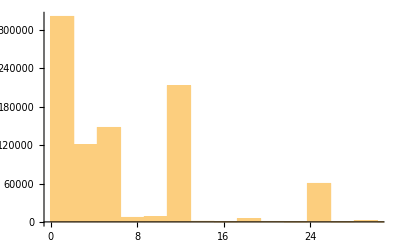

```mathematica
invoice[Histogram,"Bottles_Sold"]
```

If wanted we can adjust the bin counts

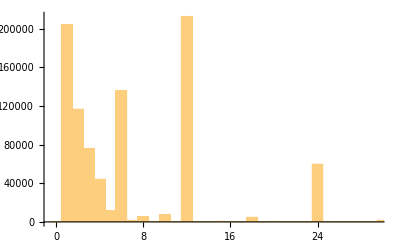

```mathematica
Histogram[invoice[All,"Bottles_Sold"],2000]
```

```mathematica
Manipulate[Histogram[invoice[Select[#,#>n&]&,"Bottles_Sold"]],{n,0,1200,100}]
```

The good thing is that it is all integer data, so we can calculate Mean, Standard deviation, min and max

```mathematica
invoice[#,"Bottles_Sold",N]&/@{Mean,StandardDeviation,Min,Max}
```

{9.87565,22.4892,0.,2160.}

0 bottles sold is strange, so let us check those specific invoices

```mathematica
Select[invoice,#["Bottles_Sold"]==0&]//Length
```

73

```mathematica
Select[invoice,#["Bottles_Sold"]==0&]
```

```mathematica
invoice[Counts,"Address"]
```

```mathematica
invoice[Counts,"Store_Name"]
```

So we can see there are 98 stores

We can quickly see which ones were the ones with the lowest number of sales and the largest

```mathematica
Sort[invoice[Counts,"Store_Name"]]
```

Let us check the sales at the Artisan Craft Soda store

```mathematica
Select[invoice,#["Store_Name"]=="Artisan Craft Soda"&]
```

```mathematica
Select[itemInvoice,#["Store_Name"]=="Artisan Craft Soda"&]
```

Let us go back to the invoice data

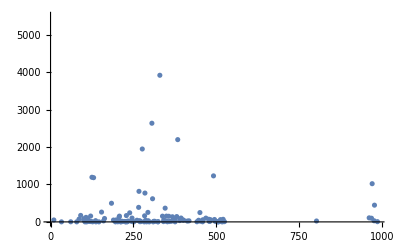

```mathematica
ListPlot[invoice[Counts,"Vendor_id"]]
```

It seems like most of the vendors are under the 4000 count in sales

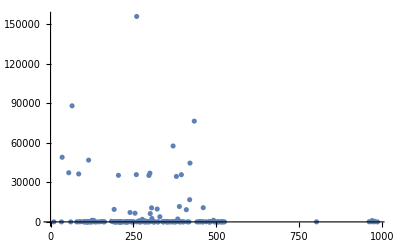

```mathematica
ListPlot[invoice[Counts,"Vendor_id"],PlotRange->All]
```

Although a few of them are way past that number

```mathematica
Max[invoice[Counts,"Vendor_id"]]
```

156106

```mathematica
Select[invoice[Counts,"Vendor_id"]//Normal,#==156106&]
```

<|260→156106|>

```mathematica
invoice[Select[#,#["Vendor_id"]==260&]&]
```

Dataset[<>]

Inuyasha brands having the biggest number of sales

```mathematica
item[[2000,1]]
```

43034

### Item

Let’s look at the data we could work with

```mathematica
Head/@item[[1]]
```

we can look at the different possible pack numbers

```mathematica
KeySort[item[Counts,"Pack"]]
```

Different Categories

```mathematica
Sort[item[Counts,"Category"]]
```

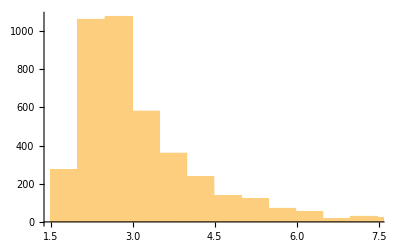

```mathematica
item[Histogram,"Bottle_Cost"]
```

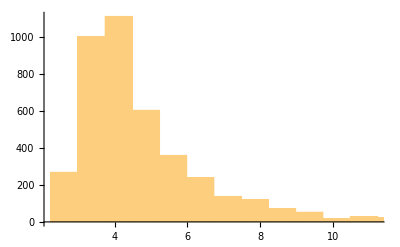

```mathematica
item[Histogram,"Bottle_Retail_Price"]
```

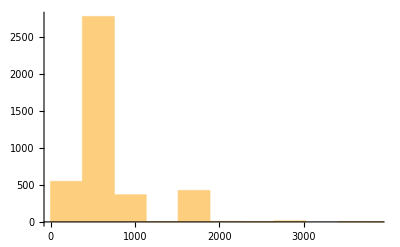

```mathematica
item[Histogram,"Bottle_Volume_ml"]
```

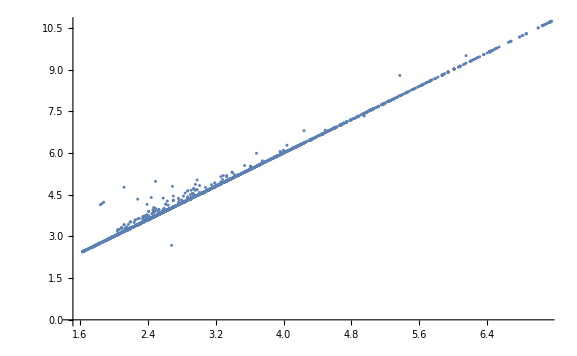

```mathematica
item[ListPlot,{"Bottle_Cost","Bottle_Retail_Price"}]
```

```mathematica
item[Max,"Bottle_Volume_ml"]
```

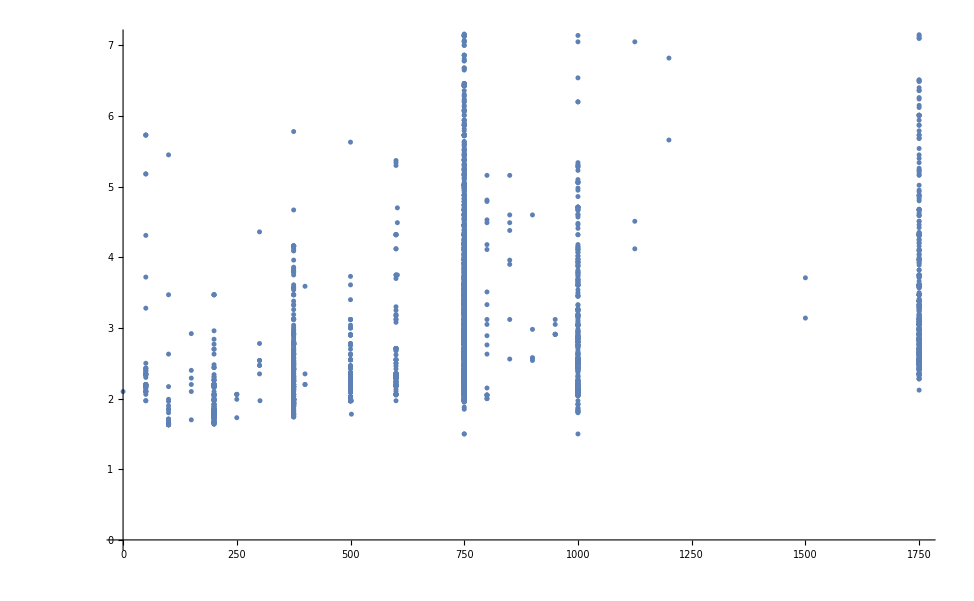

```mathematica
item[ListPlot,{"Bottle_Volume_ml","Bottle_Cost"}]
```

We can plot the whole spectrum

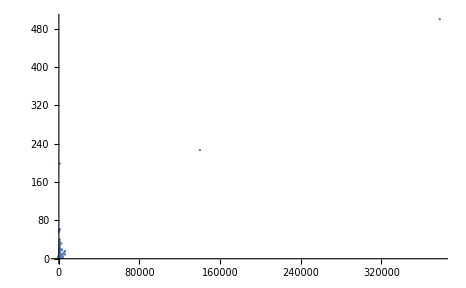

```mathematica
ListPlot[item[All,{"Bottle_Volume_ml","Bottle_Cost"}],PlotRange->All]
```

But we really loose interesting information

```mathematica
data=item[All,{"Bottle_Cost","Bottle_Retail_Price"}]//Normal//Values;
```

```mathematica
LinearModelFit[item[All,{"Bottle_Cost","Bottle_Retail_Price"}]//Normal//Values,{1,x},x]
```

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

LinearModelFit[{{4.32,6.48},{3.33,5.},{10.3,20.1},{4.44,6.66},{3.12,4.68},{3.92,5.88},{3.62,5.43},{2.77,4.16},{2.77,4.16},{2.77,4.16},{2.84,4.26},{3.48,5.22},{2.91,4.36},{4.32,6.48},{2.98,4.47},{2.54,3.81},{3.69,5.54},{3.96,5.94},4130,{2.16,3.24},{9.48,14.22},{3.94,5.91},{500.,750.},{2.35,3.53},{3.58,5.37},{3.86,5.79},{8.55,12.82},{9.,13.5},{40.25,60.38},{3.54,5.31},{19.99,29.99},{6.08,9.12},{12.6,18.9},{4.27,6.41},{5.87,8.81},{3.72,5.58},{6.81,10.22}},{1,x},x]
 |  |  |  |

```mathematica
Counts[Map[Head,data,{2}]]
```

<|{Real,Real}→4163,{Real,String}→3|>

```mathematica
DeleteCases[data,{_Real,_String}]
```

```mathematica
Counts[Map[Head,DeleteCases[data,{_Real,_String}],{2}]]
```

<|{Real,Real}→4163|>

```mathematica
model=LinearModelFit[DeleteCases[data,{_Real,_String}],{1,x},x]
```

FittedModel[0.0104165+1.49998 x]

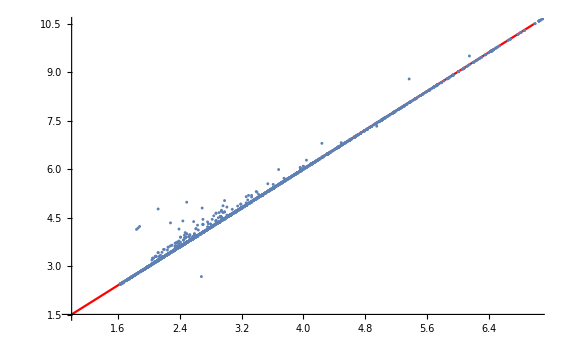

```mathematica
Show[Plot[model[x],{x,1,7},PlotStyle->Red],item[ListPlot,{"Bottle_Cost","Bottle_Retail_Price"}]]
```

```mathematica
Position[data,{_Real,_String}]
```

{{2176},{2355},{2475}}

```mathematica
item[[{2176,2355,2475}]]
```

```mathematica
Position[item[All,"Category"],""]
```

{{3},{3603},{3604},{3605}}

```mathematica
#["Item_Description"]&/@item[[{3,3603,3604,3605}]]
```

```mathematica
Normal@%
```

{Yummy Surstromming Juice,Miku's Leek Juice,Dark Fantasy,Butterbeer}

```mathematica
item[Counts,"Category"]
```

```mathematica
Length[item]
```

4166

```mathematica
item[[19]]
```

```mathematica
item[Union,"Item_Description"]//Length
```

4166

```mathematica
Length[item]
```

4166

## Observations

The cost price relationship is roughly linear as  price ~ 0.0104165+1.49998 Cost

There are 12 different categories of drink and some are not labeled into a category (Yummy Surstromming Juice, Miku’s Leek Juice, Dark Fantasy, Butterbeer)